# Dynamic Mode Decomposition for Solution to ABS Cauchy Problem

## Solution to Cauchy Problem

```mathematica
ClearAll["Global`*"];

(*parameters*)
w=1.0;
q=20.0;
n=4*256;                        (*try 256 first;can raise later*)
sgrid=Subdivide[0.,1.,n-1];
ds=sgrid[[2]]-sgrid[[1]];

(*initial conditions*)
a0=ConstantArray[1.0,n];
d0=ConstantArray[0.0,n];

(*2nd-order finite-difference derivative in s*)
Ds[v_?VectorQ]:=Module[{dv=ConstantArray[0.,Length[v]]},dv[[1]]=(-3 v[[1]]+4 v[[2]]-v[[3]])/(2 ds);(*forward*)dv[[-1]]=(3 v[[-1]]-4 v[[-2]]+v[[-3]])/(2 ds);(*backward*)Do[dv[[j]]=(v[[j+1]]-v[[j-1]])/(2 ds),{j,2,n-1}];(*centered*)dv];

(*constant-wake integral operator:F(s0)=0*)
FfromA[a_?VectorQ]:=w ds (Accumulate[a]-a[[1]]);  (*ensures F(0)=0*)

(*ODE RHS in θ for y={a1..an,d1..dn}*)
rhs[y_?VectorQ]:=Module[{a,d,as,ds1,F},a=y[[1;;n]];
d=y[[n+1;;2 n]];
(*enforce boundary matching d(θ,0)=d(θ,1)=0 strongly*)d[[1]]=0.;d[[-1]]=0.;
as=Ds[a];
ds1=Ds[d];
F=FfromA[a];
Join[(1/(2 Pi)) ds1+I F,(*a_θ*)(2/Pi) as+I q d            (*d_θ*)]];

y0=Join[a0,d0];

solY=NDSolveValue[{y'[θ]==rhs[y[θ]],y[0]==y0},y,{θ,0,20 Pi},Method->{"StiffnessSwitching"},AccuracyGoal->6,PrecisionGoal->6];

(*convenience:interpolating functions a(θ,s),d(θ,s)*)
aFun[θ_?NumericQ,s_?NumericQ]:=Module[{avec},avec=solY[θ][[1;;n]];
Interpolation[Transpose[{sgrid,avec}],InterpolationOrder->1][s]];

dFun[θ_?NumericQ,s_?NumericQ]:=Module[{dvec},dvec=solY[θ][[n+1;;2 n]];
Interpolation[Transpose[{sgrid,dvec}],InterpolationOrder->1][s]];

xpFun[θ_?NumericQ,s_?NumericQ]:=aFun[θ,s]+0.5 dFun[θ,s];
xmFun[θ_?NumericQ,s_?NumericQ]:=aFun[θ,s]-0.5 dFun[θ,s];

xcentroid [θ_,s_]:=0.5*(xpFun[θ,s]+xmFun[θ,s]);

logAbsXp[θ_,s_]:=Log[Abs[xpFun[θ,s]]];
logAbsXm[θ_,s_]:=Log[Abs[xmFun[θ,s]]];

argXp[θ_,s_]:=Arg[xpFun[θ,s]];
argXm[θ_,s_]:=Arg[xmFun[θ,s]];
```

## DMD to extract from numerical solution

```mathematica
(*----snapshot times in theta----*)
θ0=5.Pi;θ1=20. Pi;
m=1000;                         (*number of snapshots*)
θlist=Subdivide[θ0,θ1,m-1];
Δθ=θlist[[2]]-θlist[[1]];

yVec[θ_?NumericQ]:=Module[{y=solY[θ],a,d},a=y[[1;;n]];
d=y[[n+1;;2 n]];
d[[1]]=0.;d[[-1]]=0.;
Join[a,d]                 (*size 2n*)];

Y=Transpose@(yVec/@θlist);   (*(2n) x m*)

Y1=Y[[All,1;;-2]];
Y2=Y[[All,2;;-1]];
```

```mathematica
{Ufull,Σfull,Vfull}=SingularValueDecomposition[Y1];
σy=Diagonal[Σfull];
cum=Accumulate[σy^2]/Total[σy^2];
r=First@FirstPosition[cum,_?(#>=0.9999999&)]
```

10

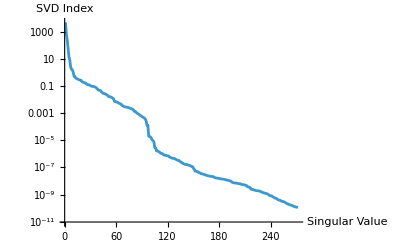

```mathematica
ListLinePlot[σy,ScalingFunctions->"Log",PlotRange->All,AxesLabel->{"Singular Value","SVD Index"}]
```

```mathematica
{U,Σ,V}=SingularValueDecomposition[Y1,r];

Σpinv=PseudoInverse[Σ];
Atilde=ConjugateTranspose[U].Y2.V.Σpinv;    (*r x r*)

{λ,W}=Eigensystem[Atilde];   (*λ:length r,W:r x r (vecs as rows or cols?)*)

Λ=DiagonalMatrix[λ];
Wmat=Transpose[W];            (*make eigenvectors columns*)
Φ=Y2.V.Σpinv.Wmat;            (*(2n) x r*)

ω=Log[λ]/Δθ;
growth=Re[ω];
freq=Im[ω];    (*rad per theta*)

y1=Y[[All,1]];
b=LeastSquares[Φ,y1];
```

```mathematica
yHat[j_Integer]:=Φ.(b*(λ^j));     (*(2n)-vector*)

(*example:compare snapshot j*)
jtest=200;
relErrJ=Norm[yHat[jtest]-Y[[All,jtest+1]]]/Norm[Y[[All,jtest+1]]];
relErrJ
```

0.000283239

```mathematica
Dimensions/@{Y1,U,Σ,V,Atilde,Φ}
```

{{2048,999},{2048,10},{10,10},{999,10},{10,10},{2048,10}}

```mathematica
Φa=Φ[[1;;n,All]];          (*centroid/‘a’ part of modes*)
Φd=Φ[[n+1;;2 n,All]];      (*‘d’ part of modes*)
```

```mathematica
jmax=Dimensions[Y][[2]]-1;
errs=Table[With[{ytrue=Y[[All,j+1]],yhat=Φ.(b*(λ^j))},Norm[yhat-ytrue]/Norm[ytrue]],{j,0,jmax}];
```

{0.0004541,0.00160481}

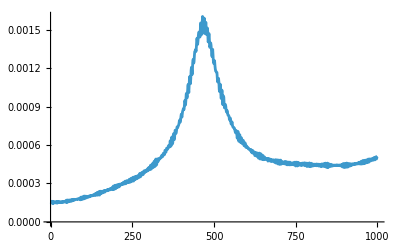

```mathematica
{Median[errs],Max[errs]}
ListLinePlot[errs,PlotRange->All]
```

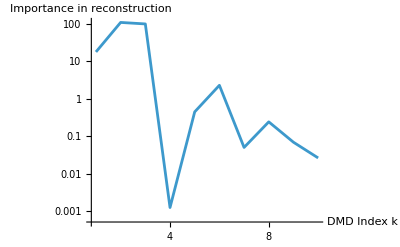

```mathematica
(*----Look at importance of modes----*)
impA=Abs[b]*(Norm/@Transpose[Φa]);          (*length r*)
impASorted=Reverse@Sort[impA];
kordered = Reverse[Ordering[impA]];

ListLinePlot[Transpose@{Range[r],impA},PlotRange->All,ScalingFunctions->{"Linear","Log"},AxesLabel->{"DMD Index k","Importance in reconstruction"}]
```

```mathematica
(*----snapshot times in theta----*)
θref=θ0;   

timeFactor[k_Integer,θ_?NumericQ]:=b[[k]]*Exp[ω[[k]]*(θ-θref)];

nTurns=23;
θstrobes=θref+2 Pi Range[0,nTurns];

modeA[k_Integer]:=Interpolation[Transpose[{sgrid,Φa[[All,k]]}],InterpolationOrder->1];

(* Calculate amplification coefficients *)
amplificationks = Table[Abs[modeA[l][1]/modeA[l][0]],{l,Range[r]}];

modeContribution[k_Integer,θ_?NumericQ,s_?NumericQ]:=Re[modeA[k][s]*timeFactor[k,θ]];
```

```mathematica
plots=Table[
ListLinePlot[Table[Table[{s,modeContribution[k,θ,s]},{s,sgrid}],{θ,θstrobes}],
PlotStyle->Directive[Black,Thick],PlotRange->All,AxesLabel->{"s",None},
PlotLabel->Row[{"k=",k,",  Importance=",ScientificForm[impA[[k]],3],", Amplification=",NumberForm[amplificationks[[k]],{3,3}]}]],{k,kordered}
];
```

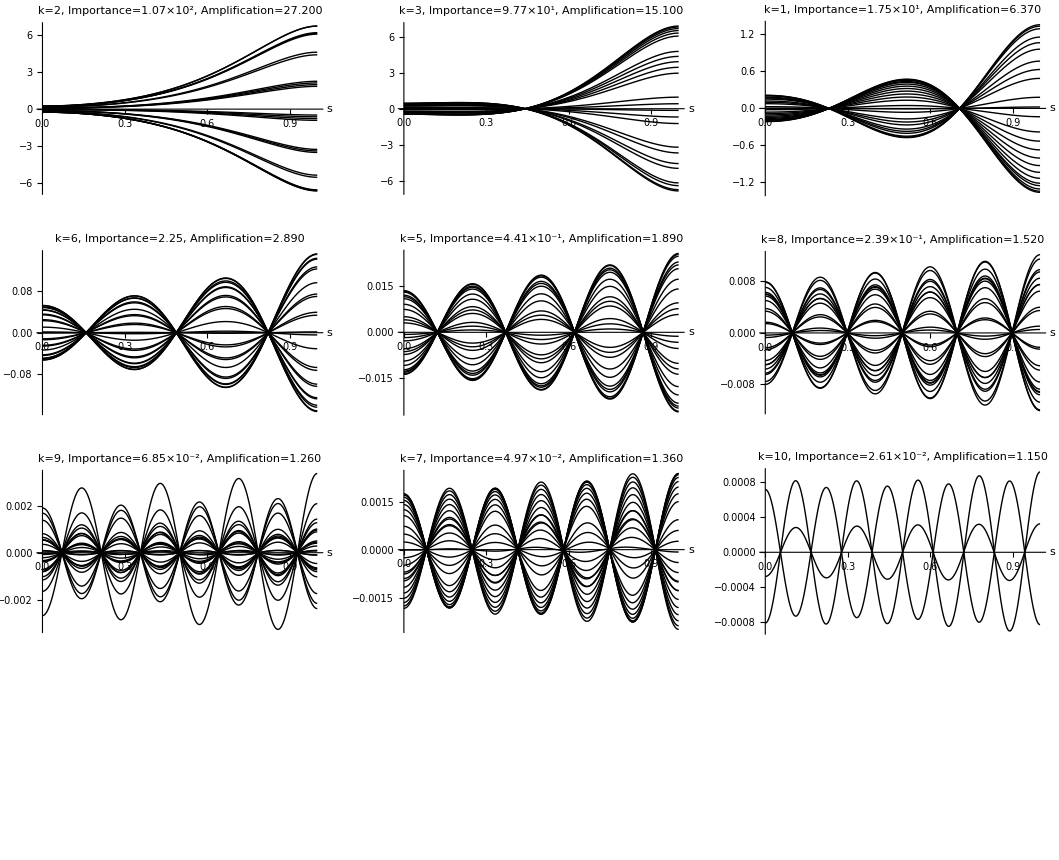

```mathematica
GraphicsGrid[Partition[plots,UpTo[3]]]
```

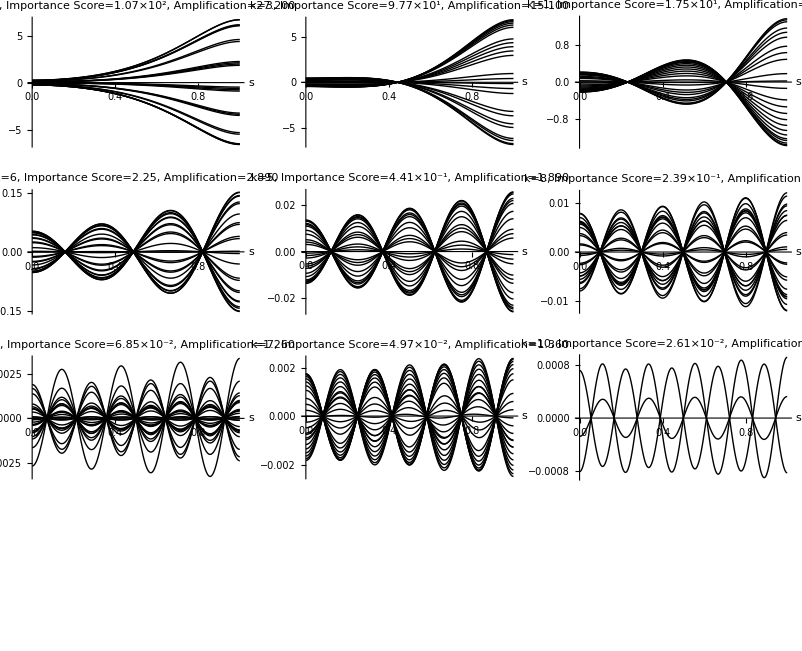

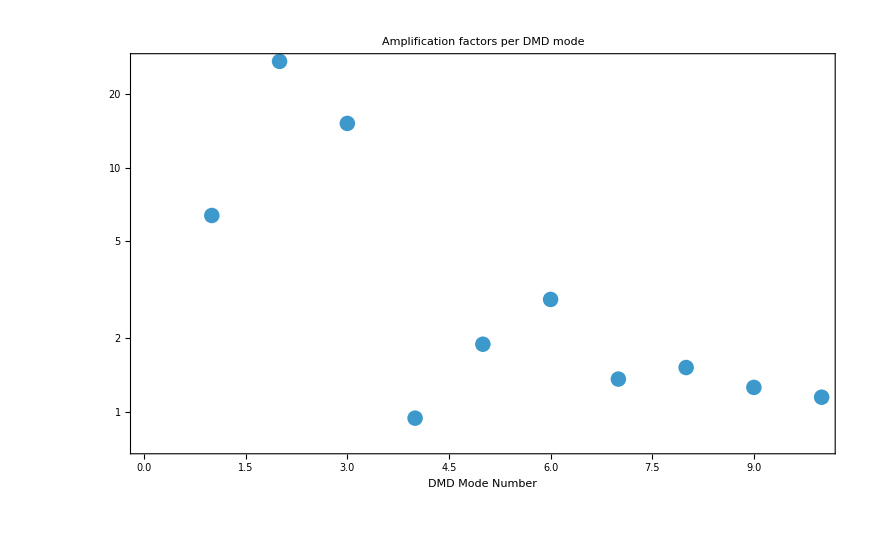

```mathematica
(* Plot amplification factors *)
ListLogPlot[Transpose[{kordered,amplificationks[[kordered]]}],
Frame->{True,True,False,False},
FrameLabel->{Style["DMD Mode Number", Black, Large],""}, LabelStyle->Directive[Larger,Black],
PlotLabel->Style["Amplification factors per DMD mode", Black, Larger], PerformanceGoal->"Speed"]
```

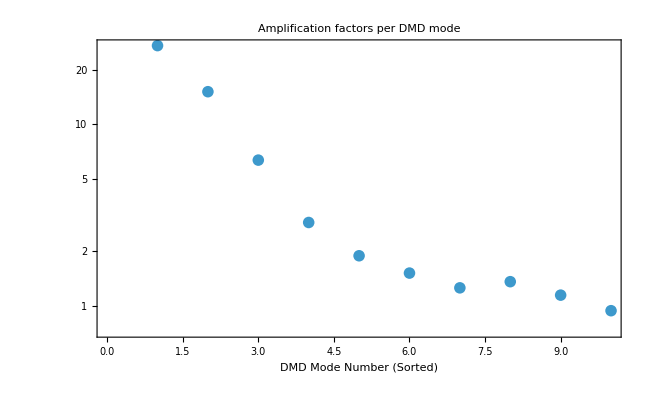

```mathematica
(* Plot amplification factors *)
ListLogPlot[Transpose[{Range[r],amplificationks[[kordered]]}],
Frame->{True,True,False,False},
FrameLabel->{Style["DMD Mode Number (Sorted)", Black, Large],""}, LabelStyle->Directive[Larger,Black],
PlotLabel->Style["Amplification factors per DMD mode", Black, Larger], PerformanceGoal->"Speed"]
```